# Discontinuous Galerkin

## Nodal Formulation

By Manuel A. Diaz, NTU, 2012.07.29

```mathematica
Quit[]; (* to reset Mathematica kernel *)
```

#### Change Notebook Background

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[0.1,0.1,0.1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[170/255,240/255,140/255]]
```

#### Set Notebook background back to default

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[1,1,1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[0,0,0]]
```

## Discretization of I_j

### Discretization in one-dimension

Now assume that we are interested on using these polynomials in conjuction with a Legendre-Gauss-Lobatto (LGL) quadrature in our interval I_j.
We first the original 4 points gauss Lobatto quadrature info for a traditional interval of [-1,1]

```mathematica
abscissas = {-1,1/Sqrt[5],-1/Sqrt[5],1}; weights={1/6,5/6,5/6,1/6};
```

Now, we wish to scale them to fit in I_j. We mutiply our abscissas by factor Δx_j/2 or a jacobian, J, transformation term in higher dimensions, and weight would remain the same:

```mathematica
{Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3],Subscript[ξ, 4]}  = abscissas; (* also the local coordinates inside Subscript[I, j] *)
{Subscript[w, 1],Subscript[w, 2],Subscript[w, 3],Subscript[w, 4]}=weights;
```

As an example, here I’ll assume and a random interval with left and right boundaries located at [1/3,2/3]. First we proceed to create the corresponding local nodes inside the cell:

```mathematica
Subscript[x, l] = 1/3; Subscript[x, r] =2/3; Subscript[Δx, j]=Subscript[x, r]-Subscript[x, l];Subscript[x, j] = (Subscript[x, l]+Subscript[x, r])/2; {Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4]}= Subscript[x, j]+Subscript[Δx, j]/2 abscissas
```

Set::shape: Lists {x_1, x_2, x_3, x_4} and 1/2 + abscissas/6 are not the same shape.

1/2+abscissas/6

Therefore we can perform now any integration over I_jin simple numerical way, example

```mathematica
N[∫_Subscript[x, l]^Subscript[x, r] Sin[𝓍]ⅆ𝓍 ,12]
```

0.159069685538

compare to its numerical counter part:

```mathematica
N[Subscript[Δx, j]/2∑_(i=1)^4 Subscript[w, i] Sin[Subscript[x, i]] ,12]
```

0.159069685393

### Discretization in two-dimensions and generalization

#### Quadrilateral element

Let us take advantage of the 1D case and use the same set of LGL quadrature points but in this case we will perfrom it first over a quadrilateral element with vertices located at,

Coordiantes for the reference quadrilateral element,

```mathematica
({{Subscript[x, 1], Subscript[y, 1]}, {Subscript[x, 2], Subscript[y, 2]}, {Subscript[x, 3], Subscript[y, 3]}, {Subscript[x, 4], Subscript[y, 4]}}) = ({{-1, -1}, {-1, 1}, {1, 1}, {1, -1}});
```

```mathematica
Plot3D[Sin[2 π x]Cos [2 π y],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

Exact integration

```mathematica
∫_-1^1 ∫_-1^1 Sin[2π x]Cos[2π y]ⅆxⅆy
```

0

Numerical Integration

```mathematica
abscissas = {-1,1/Sqrt[5],-1/Sqrt[5],1}; weights={1/6,5/6,5/6,1/6};
```

```mathematica
{Subscript[w, 1],Subscript[w, 2],Subscript[w, 3],Subscript[w, 4]} = weights; {Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3],Subscript[ξ, 4]}= abscissas;
```

scaling for the x direction

```mathematica
a =-1; b = 1; Δx = b-a;Subscript[x, c] = (b+a)/2; {Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4]} = Subscript[x, c]+ Δx/2 abscissas;
```

scaling for the y direction

```mathematica
c=-1; d = 1; Δy = d-c; Subscript[y, c] = (d+c)/2; {Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],Subscript[y, 4]} = Subscript[y, c]+ Δy/2 abscissas;
```

```mathematica
Δx/2 Δy/2∑_(i=1)^4 ∑_(j=1)^4 Subscript[w, i] Subscript[w, j] Sin[2π Subscript[x, i]]Cos[2 π Subscript[y, i]]
```

0

#### Triangular element

Coordiantes for the Triangular elements,

```mathematica
({{Subscript[x, 1], Subscript[y, 1]}, {Subscript[x, 2], Subscript[y, 2]}, {Subscript[x, 3], Subscript[y, 3]}}) = ({{-1, -1}, {1, -1}, {-1, 1}});
```

```mathematica
Plot3D[Sin[2 π x]Cos [2 π y],{x,0,1},{y,0,1-x}]
```

-Graphics3D-

Exact integration procedure

```mathematica
∫_0^1 ∫_0^(1-x) Sin[2 π x]Cos[2 π y]ⅆxⅆy
```

0

Numerical Integration procedure

```mathematica
abscissas = {-1,1/Sqrt[5],-1/Sqrt[5],1}; weights={1/6,5/6,5/6,1/6};
```

## Translating from Legendre Coeficients, u_j^(i)(t), to nodal solution, u^h(x,t)

Here we are interested in understanding the expansion of these polynomials from a continuous form to a pieze wize for of the from.

### Initialization

#### Build Notation

```mathematica
Symbolize[Subscript[u, h]];Symbolize[u^_];
```

```mathematica
Subscript[u, 1]//InputForm
```

Subscript[u, 1]

```mathematica
u^(l) // InputForm
```

u⎵Superscript⎵LeftParenthesis⎵l⎵RightParenthesis

```mathematica
Table[ToExpression[RowBox[{"{",ToString[i],"}"}]],{i,10}]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}

```mathematica
Notation[∫_Subscript[I, j] f_ⅆx_ ⟹ Integrate[f_,{x_,-Subscript[Δx, j]/2,Subscript[Δx, j]/2}]]
```

#### Case1: assume the Riemann IC:

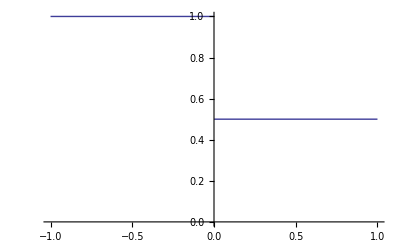

```mathematica
u[x_,t_]:= Piecewise[{{1,x<0},{0.5,x>=0}}];
Plot[u[x,t],{x,-1,1},PlotRange->{0,1}]
```

#### Case2: assume Sinusoidal wave function :

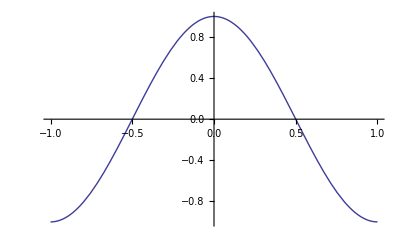

```mathematica
u[x_,t_]:= Cos[π x];
Plot[u[x,t],{x,-1,1},PlotRange->Full]
```

### Method 1: Traditional Way

#### Degrees of Freedom u_j^(l)

For u_j element using the continuous function u(x,t). If we define the degrees of freedom as:

u_j^(l) = u_j^(l)[t] = 1/Δx_j^(l+1)∫_I_j u[x,t] v_l^(j)[x]ⅆx, for l = 1,...,k

of course, we need to define u[x,t] in order to continue. We traditionally have two choises a continuous or a discontinuous function,

Therefore :

```mathematica
{u^(0),u^(1),u^(2),u^(3),u^(4),u^(5),u^(6)} = Table[ 1/Subscript[Δx, j]^(l+1)∫_Subscript[I, j] (u[x,t] Subscript[v, l])ⅆx,{l,0,6}];
```

```mathematica
{u^(0),u^(1),u^(2),u^(3),u^(4),u^(5),u^(6)} //MatrixForm
```

(0.75
-0.0625
0.
0.0015625
0.
-0.000062004
0.)

#### Solution Approximation u_h

```mathematica
Quit[];
```

And the approximation of the solution u(x,t) as u_h, is defined as follows

u^h[x,t] = ∑_(l=0)^k a_l u_j^(l)[t]v_l^(j)[x], for x ∈ I_j

here a_l are contants values found to normalize the contribution of each polinomial.

for the Modal formulation the expasion is of the form

```mathematica
Np = 4;
ClearAll[sum]
```

```mathematica
sum[x_,t_,n_Integer?Positive]:=Array[Subscript[u[t], #] Subscript[v[x], #]&,n,1,Defer[Plus[##]]&]
```

```mathematica
Subscript[u, h][x_,t_] := sum[x,t,Np]
```

```mathematica
Subscript[u, h][a,b]
```

u[b]_1 v[a]_1+u[b]_2 v[a]_2+u[b]_3 v[a]_3+u[b]_4 v[a]_4

for the Nodal formulation the expansion is of the form

```mathematica
Np = 5;
ClearAll[sum]
```

```mathematica
sum[x_,t_,n_Integer?Positive]:=Array[Subscript[u[x,t], #] Subscript[v[x], #]&,n,1,Defer[Plus[##]]&]
```

```mathematica
Subscript[u, h][x_,t_] := sum[x,t,Np]
```

```mathematica
Subscript[u, h][a,b]
```

u[a,b]_1 v[a]_1+u[a,b]_2 v[a]_2+u[a,b]_3 v[a]_3+u[a,b]_4 v[a]_4+u[a,b]_5 v[a]_5

Following the last example we can proceed to compute from the degress of freedom the approximate solution u_h,

```mathematica
NSum[Subscript[a, l] u^(l)Subscript[v, l],{l,0,3}]
```

NSum::nsnum: Summand (or its derivative) a_l\ u^l\ v_l is not numerical at point l = 0.

NSum[a_l u^l v_l,{l,0,3}]

### Method 2: The Vandermonde Matrix

#### Degrees of Freedom u_j^(l)

From previous calculations we can do:

```mathematica
Table[Subscript[v, i]= Expand[Subscript[p, i]],{i,0,6}];(* recall that z -> (x-Subscript[x, j])/Subscript[Δx, j] *)
Table[Subscript[v, i],{i,0,6}]//MatrixForm
```

(1
z
-1/12+z^2
-(3 z)/20+z^3
3/560-(3 z^2)/14+z^4
(5 z)/336-(5 z^3)/18+z^5
-5/14784+(5 z^2)/176-(15 z^4)/44+z^6)

Evaluating every escaled polynomial for the computed abcsissas we get:

```mathematica
vandermonde = Table[Subscript[v, n]/.z->Subscript[x, m],{m,1,4},{n,0,3}];
vandermonde //MatrixForm
```

(1 | 1/3 | 1/36 | -7/540
1 | 1/2+1/(6 √5) | -1/12+(1/2+1/(6 √5))^2 | -3/20 (1/2+1/(6 √5))+(1/2+1/(6 √5))^3
1 | 1/2-1/(6 √5) | -1/12+(1/2-1/(6 √5))^2 | -3/20 (1/2-1/(6 √5))+(1/2-1/(6 √5))^3
1 | 2/3 | 13/36 | 53/270)

if for the case every we are using equally distributed cells, we can just program the numerical version of this matrix:

```mathematica
vandermonde //MatrixForm//N
```

(1. | 0.333333 | 0.0277778 | -0.012963
1. | 0.574536 | 0.246758 | 0.103469
1. | 0.425464 | 0.0976866 | 0.0131979
1. | 0.666667 | 0.361111 | 0.196296)

#### Solution Approximation u_h

## Math Objects

Math Objects that we are going to be dealing with in Nodal DG

### Mass Matrix

Well this one is very simple, if we are using legendre polynomial as our base fucntion, we have done this manny times by now,

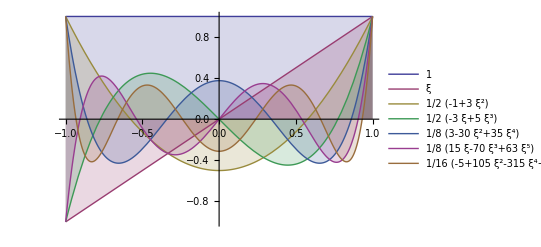

```mathematica
legendreP =Table[LegendreP[i,ξ],{i,0,6}];Table[Subscript[P, i]=legendreP[[i+1]],{i,0,6}];
Plot[Evaluate[legendreP],{ξ,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

The mass matrix, M, is then defined as

```mathematica
M = Table[∫_-1^1 Subscript[P, i] Subscript[P, j] ⅆξ,{i,0,6},{j,0,6}];M//Simplify//MatrixForm
```

(2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2/3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2/5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2/7 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2/9 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2/11 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2/13)

and

```mathematica
invM = Inverse[M];invM//Simplify//MatrixForm
```

(1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 5/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 7/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 9/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 11/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 13/2)

### Stiffness Matrix

```mathematica
Clear[x]; dLegendreP[j_,x_]:= D[LegendreP[j,x], x];
```

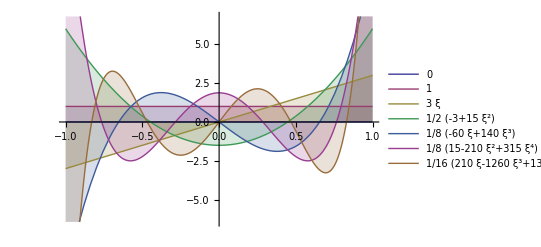

```mathematica
dlegendreP = Table[dLegendreP[i,ξ],{i,0,6}];
Table[Subscript[dP, i]=dLegendreP[i,ξ],{i,0,6}];
Plot[Evaluate[dlegendreP],{ξ,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
S = Table[∫_-1^1 Subscript[P, i] Subscript[dP, j] ⅆξ,{i,0,6},{j,0,6}];S//Simplify//MatrixForm
```

(0 | 2 | 0 | 2 | 0 | 2 | 0
0 | 0 | 2 | 0 | 2 | 0 | 2
0 | 0 | 0 | 2 | 0 | 2 | 0
0 | 0 | 0 | 0 | 2 | 0 | 2
0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0)

#### Is there any relation between M and S?

Lets explore the case that M = α.S:

```mathematica
Dr = invM.S; Dr //MatrixForm
```

(0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 0 | 3 | 0 | 3 | 0 | 3
0 | 0 | 0 | 5 | 0 | 5 | 0
0 | 0 | 0 | 0 | 7 | 0 | 7
0 | 0 | 0 | 0 | 0 | 9 | 0
0 | 0 | 0 | 0 | 0 | 0 | 11
0 | 0 | 0 | 0 | 0 | 0 | 0)

An Amazing relation!

### Vandermonde Matrix

In Nodal DG this is our most important interpolation tool and the key to translate nodal information to legendre coeficients and viceversa. The Vandermonde matrix is defined as,

```mathematica
Vandermonde =  Table[LegendreP[n,Subscript[x, i]],{i,1,5},{n,0,4}]; Vandermonde//MatrixForm
```

(1 | x_1 | 1/2 (-1+3 x_1^2) | 1/2 (-3 x_1+5 x_1^3) | 1/8 (3-30 x_1^2+35 x_1^4)
1 | x_2 | 1/2 (-1+3 x_2^2) | 1/2 (-3 x_2+5 x_2^3) | 1/8 (3-30 x_2^2+35 x_2^4)
1 | x_3 | 1/2 (-1+3 x_3^2) | 1/2 (-3 x_3+5 x_3^3) | 1/8 (3-30 x_3^2+35 x_3^4)
1 | x_4 | 1/2 (-1+3 x_4^2) | 1/2 (-3 x_4+5 x_4^3) | 1/8 (3-30 x_4^2+35 x_4^4)
1 | x_5 | 1/2 (-1+3 x_5^2) | 1/2 (-3 x_5+5 x_5^3) | 1/8 (3-30 x_5^2+35 x_5^4))

where x_i are the nodes coordinates inside our element.
The rules of the game goes as follows:

u_coef = inv[V].u_nodes,   and viceversa     u_nodes = [V].u_coef

It is important to realize that in nodal DG we use Lagrange Polynomials to interpolate data at their respectives nodes (like we do in FEM). How good this interpolation is done? well we rely on the interpolated data from the Legrendre Expansion as the core Idea behind the method.

### Relations of the Nodal data and the Modal data (Legendre Coefs)

The first tool that we need is in our toolbox is how derivate a function us expansion on Legendre Coeficients,

Let us define any function F, e.g.:

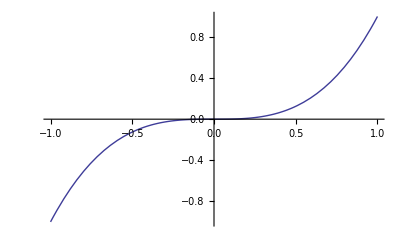

```mathematica
F[x_] := x^3; Plot[F[ξ],{ξ,-1,1}]
```

and it’s derivate,

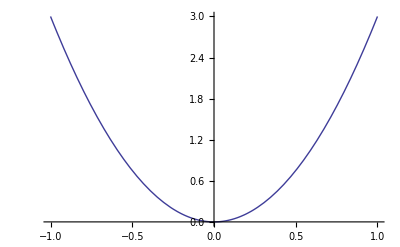

```mathematica
dF[x_] := 3x^2; Plot[dF[ξ],{ξ,-1,1}]
```

Second. We know need a discrete domain to compute this information, let’s use

Chevishev nodes

```mathematica
x = Table[ i,{i,-1,1,1/2}]
```

{-1,-1/2,0,1/2,1}

```mathematica
Table[Subscript[ξ, i] = Sin[1/2 π x[[i]]],{i,1,5}] (* nodes in a standard element *)
```

{-1,-1/(√2),0,1/(√2),1}

```mathematica
Subscript[f, nodes] = Table[F[Subscript[ξ, i]],{i,1,5}]
```

{-1,-1/(2 √2),0,1/(2 √2),1}

```mathematica
Subscript[df, nodes] =Table[dF[Subscript[ξ, i]],{i,1,5}]
```

{3,3/2,0,3/2,3}

Lets translate our nodal information to Legendre coefficients, build our vandermonde Matrix,

```mathematica
V =  Table[LegendreP[n,Subscript[ξ, i]],{i,1,5},{n,0,4}]; V//MatrixForm
```

(1 | -1 | 1 | -1 | 1
1 | -1/(√2) | 1/4 | 1/(4 √2) | -13/32
1 | 0 | -1/2 | 0 | 3/8
1 | 1/(√2) | 1/4 | -1/(4 √2) | -13/32
1 | 1 | 1 | 1 | 1)

and it’s Inverse, invV,

```mathematica
invV = Inverse[V]; invV//MatrixForm
```

(1/30 | 4/15 | 2/5 | 4/15 | 1/30
-1/10 | -(2 √2)/5 | 0 | (2 √2)/5 | 1/10
5/21 | 4/21 | -6/7 | 4/21 | 5/21
-2/5 | (2 √2)/5 | 0 | -(2 √2)/5 | 2/5
8/35 | -16/35 | 16/35 | -16/35 | 8/35)

Then let us compute our Legendre coeficients, f_coef,

```mathematica
Subscript[f, coef]= invV.Subscript[f, nodes]
```

{0,3/5,0,2/5,0}

#### Here we have an intermission to ask ourselves:

Is there any way I can find a parameter α such that,

[V^-1dF/dξ] = α . [V^-1F ]

in words: such that the legendre coeficients of the function derivative can be directly computed with the legendre coeficients of the original Function?

Let’s explore this possibility:

```mathematica
Subscript[df, coef] = invV.Subscript[df, nodes]
```

{1,0,2,0,0}

This last results will be our objetive,

Note the relation between M and S, and let us built this relation for our model problem

```mathematica
Dr = DiagonalMatrix[{1,3,5,7,9,11},1,5]+DiagonalMatrix[{1,3,5,7,9,11},3,5]+
DiagonalMatrix[{1,3,5,7,9,11},5,5]; Dr //MatrixForm
```

(0 | 1 | 0 | 1 | 0
0 | 0 | 3 | 0 | 3
0 | 0 | 0 | 5 | 0
0 | 0 | 0 | 0 | 7
0 | 0 | 0 | 0 | 0)

now if make the comparison of results,

```mathematica
Subscript[df, coef]==Dr.Subscript[f, coef]
```

True

Wow!! we have found a nice feature that can save a lot of numerical work!

### Mass Matrix for Nodal DG

For this part let us compare our computation with the examples in the text: Nodal DG 2008.
Let us use now LGL points.

#### Legendre-Gauss-Lobatto (LGL) Polynomials

```mathematica
lobatto = Table[Subscript[P, k]-Subscript[P, k-2],{k,2,5}] //Simplify;
```

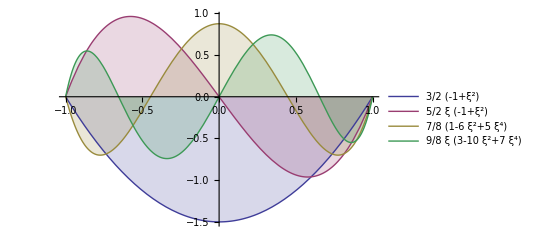

```mathematica
Plot[Evaluate[lobatto],{ξ,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
Table[Subscript[Lo, i]= lobatto[[i]],{i,1,4}]//TableForm
```

3/2 (-1+ξ^2)
5/2 ξ (-1+ξ^2)
7/8 (1-6 ξ^2+5 ξ^4)
9/8 ξ (3-10 ξ^2+7 ξ^4)

Lobatto roots and weights

```mathematica
abscissas = -Sort[List @@ Roots[Subscript[Lo, 4]==0,ξ][[All,2]],Greater];
Table[Subscript[ξ, i]=abscissas[[i]],{i,1,5}]
```

{-1,-√(3/7),0,√(3/7),1}

```mathematica
V =  Table[LegendreP[n,Subscript[ξ, i]],{i,1,5},{n,0,4}]; V//MatrixForm
```

(1 | -1 | 1 | -1 | 1
1 | -√(3/7) | 1/7 | (3 √(3/7))/7 | -3/7
1 | 0 | -1/2 | 0 | 3/8
1 | √(3/7) | 1/7 | -(3 √(3/7))/7 | -3/7
1 | 1 | 1 | 1 | 1)

```mathematica
Subscript[M, nodal]=Inverse[V.Transpose[V]]; Subscript[M, nodal]//N//MatrixForm
```

(0.25 | -0.138038 | -0.0977778 | 0.0758157 | -0.04
-0.138038 | 0.901358 | -0.324938 | -0.241975 | 0.0758157
-0.0977778 | -0.324938 | 1.20099 | -0.324938 | -0.0977778
0.0758157 | -0.241975 | -0.324938 | 0.901358 | -0.138038
-0.04 | 0.0758157 | -0.0977778 | -0.138038 | 0.25)

Becuase we are using lagrange Polynomials as our base function is no surprice that the Mass matrix is a full matrix.

### Grad Vandermonde

Similarly to the Vandermonde Matrix,

```mathematica
Vr =  Table[dLegendreP[n,y]/.y->Subscript[ξ, i],{i,1,5},{n,0,4}];Vr//MatrixForm
```

(0 | 1 | -3 | 6 | -10
0 | 1 | -3 √(3/7) | 12/7 | 0
0 | 1 | 0 | -3/2 | 0
0 | 1 | 3 √(3/7) | 12/7 | 0
0 | 1 | 3 | 6 | 10)

### Dr Matrix for Nodal DG

```mathematica
Dr = Vr.Inverse[V]; Dr//N//MatrixForm
```

(-5. | 6.7565 | -2.66667 | 1.41016 | -0.5
-1.24099 | 0. | 1.74574 | -0.763763 | 0.25901
0.375 | -1.33658 | 0. | 1.33658 | -0.375
-0.25901 | 0.763763 | -1.74574 | 0. | 1.24099
0.5 | -1.41016 | 2.66667 | -6.7565 | 5.)

We are in perfect agreement with the Dr. Hestaven and Dr. Warburton ; )

Note that this matrix is Skew-antisymmetric.

### Lift Operator

Last but not least.... (pending)